## Write down the nondimensionalized Fokker-Planck equation

```mathematica
FP= D[p[t, xt, yt], t]==λt*D[yt*p[t, xt, yt], xt]+D[yt*p[t, xt, yt], yt]-D[xt*p[t, xt, yt],yt]+(αt^2/2)D[p[t, xt, yt],{xt,2}]+(αt^2/2)D[p[t, xt, yt],{yt,2}]
```

p^(1,0,0)[t,xt,yt]==p[t,xt,yt]-xt p^(0,0,1)[t,xt,yt]+yt p^(0,0,1)[t,xt,yt]+1/2 αt^2 p^(0,0,2)[t,xt,yt]+yt λt p^(0,1,0)[t,xt,yt]+1/2 αt^2 p^(0,2,0)[t,xt,yt]

## Get the steady-state variances

```mathematica
A= {{ 0,λt},{-1, 1}}
B = {{αt,0},{0,αt}}
s=Array[Y,{2,2}]
ss =( s/. Expand[FullSimplify[Solve[A.s+s.Transpose[A]==B.Transpose[B], Flatten[s]]]])[[1]]
```

{{0,λt},{-1,1}}

{{αt,0},{0,αt}}

{{Y[1,1],Y[1,2]},{Y[2,1],Y[2,2]}}

{{αt^2/2+αt^2/(2 λt)+(αt^2 λt)/2,αt^2/(2 λt)},{αt^2/(2 λt),αt^2/2+αt^2/(2 λt)}}

## Choose the parameter values

```mathematica
λts = {0.02,0.05, 0.08, 0.125,0.15};
αts = {0.3};
tfs = 5/λts
params = Flatten[Table[{λt->l, αt->a}, {l, λts}, {a, αts}], 1]
legend =  Flatten[Table["λt="<>ToString[l]<>"; "<> "αt="<>ToString[a], {l, λts},{a, αts}], 1];
```

{250.,100.,62.5,40.,33.3333}

{{λt→0.02,αt→0.3},{λt→0.05,αt→0.3},{λt→0.08,αt→0.3},{λt→0.125,αt→0.3},{λt→0.15,αt→0.3}}

## Get the trajectory of the mean

```mathematica
eig=FullSimplify[Eigenvectors[A]]
```

{{1/2 (1+√(1-4 λt)),1},{1/2 (1-√(1-4 λt)),1}}

```mathematica
Eigenvalues[A]
```

{1/2 (1-√(1-4 λt)),1/2 (1+√(1-4 λt))}

```mathematica
cstar =Re[N[ Flatten[Table[(eig[[1,1]])^-1/.p, {p, params}]]]]
```

{1.02084,1.05573,1.09612,1.17157,1.22515}

## Set up the mesh, boundary conditions, and initial condition

#### Steady-state distribution widths in x~, y~

```mathematica
xtwidths = N[Table[ss[[1,1]]/.p, {p, params}]];
ytwidths = N[Table[ss[[2,2]]/.p, {p, params}]];
xtStds =Sqrt[xtwidths]
ytStds = Sqrt[ytwidths]
```

{1.51522,0.973268,0.781729,0.6408,0.593085}

{1.51493,0.972111,0.779423,0.636396,0.587367}

```mathematica
deltaWidth = 0.2;
deltaVar = deltaWidth^2
minCell = deltaWidth/4
```

0.04

0.05

```mathematica
Sqrt[αts[[1]]^2/2]
```

0.212132

#### Boundary condition at x~* =1. Choose the boundaries to be far enough away from the initial condition and the final distribution

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
xt0 = 12;
yt0 = xt0*cstar;
xtls=-5*xtStds
xtrs = xt0+5*xtStds
ytls=cstar
ytrs = cstar*xt0+5*ytStds
```

{-7.57611,-4.86634,-3.90864,-3.204,-2.96543}

{19.5761,16.8663,15.9086,15.204,14.9654}

{1.02084,1.05573,1.09612,1.17157,1.22515}

{19.8247,17.5293,17.0505,17.2409,17.6386}

```mathematica
icPos =Transpose[{Table[xt0, 5], yt0}]
icVar ={{deltaVar, 0},{0, deltaVar}}
ic0 = N[Table[PDF[MultinormalDistribution[pos,icVar], {xt, yt}], {pos, icPos}]];
Sqrt[icVar]
bcFunc[xtl_, xtr_, ytl_, ytr_] :={
	  p[t, xtl, yt]==0,
           p[t, xtr, yt]==0,
           p[t, xt, ytr]==0,
           p[t, xt, ytl]==0
};
ΩFunc[xtl_, xtr_, ytl_, ytr_] :=ImplicitRegion[True,{{xt,xtl,xtr},{yt,ytl,ytr}}];
bcs = MapThread[bcFunc, {xtls, xtrs, ytls, ytrs}];
Ω=MapThread[ΩFunc,{xtls, xtrs, ytls, ytrs}]
meshes = Table[ToElementMesh[o, MaxCellMeasure->minCell, MaxBoundaryCellMeasure->minCell/4], {o, Ω}]
meshes[[1]]["Wireframe"]
```

{{12,12.2501},{12,12.6687},{12,13.1534},{12,14.0589},{12,14.7018}}

{{0.04,0},{0,0.04}}

{{0.2,0},{0,0.2}}

{ImplicitRegion[-7.57611≤xt≤19.5761&&1.02084≤yt≤19.8247,{xt,yt}],ImplicitRegion[-4.86634≤xt≤16.8663&&1.05573≤yt≤17.5293,{xt,yt}],ImplicitRegion[-3.90864≤xt≤15.9086&&1.09612≤yt≤17.0505,{xt,yt}],ImplicitRegion[-3.204≤xt≤15.204&&1.17157≤yt≤17.2409,{xt,yt}],ImplicitRegion[-2.96543≤xt≤14.9654&&1.22515≤yt≤17.6386,{xt,yt}]}

{ElementMesh[{{-7.57611,19.5761},{1.02084,19.8247}},{TriangleElement[<56866>]}],ElementMesh[{{-4.86634,16.8663},{1.05573,17.5293}},{TriangleElement[<44884>]}],ElementMesh[{{-3.90864,15.9086},{1.09612,17.0505}},{TriangleElement[<41632>]}],ElementMesh[{{-3.204,15.204},{1.17157,17.2409}},{TriangleElement[<39738>]}],ElementMesh[{{-2.96543,14.9654},{1.22515,17.6386}},{TriangleElement[<39572>]}]}

-Graphics-

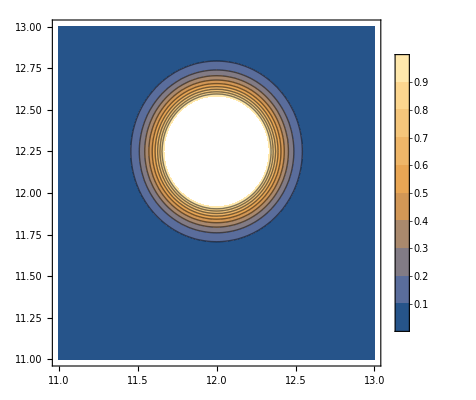

```mathematica
toPlot=1;
ContourPlot[ic0[[toPlot]], {xt, xt0-1, xt0+1}, {yt, xt0-1, xt0+1}, PlotRange->{0,1}, PlotLegends->Automatic]
```

## Calculate the time-integrated probability distribution and the flux through the boundary

```mathematica
NDSolverParams[param_, ic_, bc_, reg_, tf_] :=Module[{N},
N = NDSolve[Join[{(FP/. param),p[0, xt,yt]== ic}, bc],
                                   p,{t, 0, tf},{xt, yt}∈reg, 
Method->{"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement"}}}];
Return[(p/.N[[1]])];
]
```

```mathematica
solsIc0=MapThread[NDSolverParams, {params, ic0, bcs, meshes, tfs}];
```

```mathematica
dv = Table[Derivative[0,0,1][sol], {sol, solsIc0}];
```

```mathematica
Manipulate[Plot3D[solsIc0[[1]][t, xt, yt], {xt, 0,xtrs[[1]]}, {yt, 0,ytrs[[1]]}, AxesLabel->{xt, yt}, PlotRange->{-0.01, 0.3}, PlotLegends->Automatic, PerformanceGoal->"Quality"],{t, 0, tfs[[1]]}]
```

xtls gives the “left” boundary in x as 5 stds of the ss distribution from 0. To get the hitting distribution, integrate from there to 0+5*std

```mathematica
xranges = Table[N[Range[-1, 3, 3/50]],5]
```

{{-1.,-0.94,-0.88,-0.82,-0.76,-0.7,-0.64,-0.58,-0.52,-0.46,-0.4,-0.34,-0.28,-0.22,-0.16,-0.1,-0.04,0.02,0.08,0.14,0.2,0.26,0.32,0.38,0.44,0.5,0.56,0.62,0.68,0.74,0.8,0.86,0.92,0.98,1.04,1.1,1.16,1.22,1.28,1.34,1.4,1.46,1.52,1.58,1.64,1.7,1.76,1.82,1.88,1.94,2.,2.06,2.12,2.18,2.24,2.3,2.36,2.42,2.48,2.54,2.6,2.66,2.72,2.78,2.84,2.9,2.96},{-1.,-0.94,-0.88,-0.82,-0.76,-0.7,-0.64,-0.58,-0.52,-0.46,-0.4,-0.34,-0.28,-0.22,-0.16,-0.1,-0.04,0.02,0.08,0.14,0.2,0.26,0.32,0.38,0.44,0.5,0.56,0.62,0.68,0.74,0.8,0.86,0.92,0.98,1.04,1.1,1.16,1.22,1.28,1.34,1.4,1.46,1.52,1.58,1.64,1.7,1.76,1.82,1.88,1.94,2.,2.06,2.12,2.18,2.24,2.3,2.36,2.42,2.48,2.54,2.6,2.66,2.72,2.78,2.84,2.9,2.96},{-1.,-0.94,-0.88,-0.82,-0.76,-0.7,-0.64,-0.58,-0.52,-0.46,-0.4,-0.34,-0.28,-0.22,-0.16,-0.1,-0.04,0.02,0.08,0.14,0.2,0.26,0.32,0.38,0.44,0.5,0.56,0.62,0.68,0.74,0.8,0.86,0.92,0.98,1.04,1.1,1.16,1.22,1.28,1.34,1.4,1.46,1.52,1.58,1.64,1.7,1.76,1.82,1.88,1.94,2.,2.06,2.12,2.18,2.24,2.3,2.36,2.42,2.48,2.54,2.6,2.66,2.72,2.78,2.84,2.9,2.96},{-1.,-0.94,-0.88,-0.82,-0.76,-0.7,-0.64,-0.58,-0.52,-0.46,-0.4,-0.34,-0.28,-0.22,-0.16,-0.1,-0.04,0.02,0.08,0.14,0.2,0.26,0.32,0.38,0.44,0.5,0.56,0.62,0.68,0.74,0.8,0.86,0.92,0.98,1.04,1.1,1.16,1.22,1.28,1.34,1.4,1.46,1.52,1.58,1.64,1.7,1.76,1.82,1.88,1.94,2.,2.06,2.12,2.18,2.24,2.3,2.36,2.42,2.48,2.54,2.6,2.66,2.72,2.78,2.84,2.9,2.96},{-1.,-0.94,-0.88,-0.82,-0.76,-0.7,-0.64,-0.58,-0.52,-0.46,-0.4,-0.34,-0.28,-0.22,-0.16,-0.1,-0.04,0.02,0.08,0.14,0.2,0.26,0.32,0.38,0.44,0.5,0.56,0.62,0.68,0.74,0.8,0.86,0.92,0.98,1.04,1.1,1.16,1.22,1.28,1.34,1.4,1.46,1.52,1.58,1.64,1.7,1.76,1.82,1.88,1.94,2.,2.06,2.12,2.18,2.24,2.3,2.36,2.42,2.48,2.54,2.6,2.66,2.72,2.78,2.84,2.9,2.96}}

```mathematica
nintxsolve[xr_, s_, tf_, ystar_]:=Module[{t, x, f},
n =Table[NDSolveValue[{g'[t]==s[t, x, ystar],g[0]==0},g,{t, 0, tf},Method->{"ExplicitRungeKutta", "DifferenceOrder"->4}][tf], {x, xr}];
Return[n];
];
```

```mathematica
toIntegrate[t] = dv[[1]][t, -0.6, cstar[[1]]]
```

InterpolatingFunction[{{0., 250.}, {-7.57611, 19.5761}, {1.02084, 19.8247}}, <>][t,-0.6,1.02084]

```mathematica
NDSolveValue[{g'[t]==toIntegrate[t],g[0]==0},g,{t, 0, 250}, Method->Automatic][250]//AbsoluteTiming
```

{0.905935,0.0000375462}

```mathematica
NDSolveValue[{g'[t]==toIntegrate[t],g[0]==0},g,{t, 0, 250}, Method->{"ExplicitRungeKutta", "DifferenceOrder"->4}][250]//AbsoluteTiming
```

{0.906774,0.0000375069}

```mathematica
NDSolveValue[{g'[t]==toIntegrate[t],g[0]==0},g,{t, 0, 250}, Method->{"Extrapolation"}][250]//AbsoluteTiming
```

{0.898301,0.000037511}

```mathematica
xvals = MapThread[nintxsolve, {xranges, dv, tfs, cstar}];
```

```mathematica
X=MapThread[Interpolation[Transpose@{#1, #2*(αts[[1]]^2/2)}][x]&, {xranges, xvals}];
```

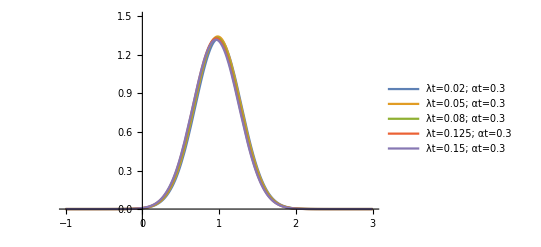

```mathematica
Plot[X, {x, -1, 3}, PlotLegends->legend, PlotRange->{-0.1, 1.5}]
```

```mathematica
IntegFunc[f_, l_, r_] := NIntegrate[f, {x, l, r}]
```

```mathematica
xls = Table[-1, 5];
xrs = Table[3, 5];
```

```mathematica
normsIc0 = MapThread[IntegFunc, {X, xls, xrs}]
corrected = MapThread[#1/#2&, {X, normsIc0}];
meansIc0= MapThread[IntegFunc, {corrected*x,xls, xrs}]
secondIc0 = MapThread[IntegFunc, {corrected*x*x, xls, xrs}]
varsIc0 = secondIc0-meansIc0^2
diffIc0 = varsIc0/meansIc0^2;
```

InterpolatingFunction::dmvali: The integration endpoint 3 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmvali will be suppressed during this calculation.

{0.997426,1.01088,1.004,1.00263,0.996353}

{0.991969,0.981256,0.972471,0.96248,0.958642}

{1.07382,1.05272,1.03574,1.01665,1.00963}

{0.0898208,0.089862,0.0900387,0.0902838,0.0906352}

```mathematica
grid = Flatten[Table[{l, a}, {l, λts}, {a, αts}], 1];
params
```

{{λt→0.02,αt→0.3},{λt→0.05,αt→0.3},{λt→0.08,αt→0.3},{λt→0.125,αt→0.3},{λt→0.15,αt→0.3}}

```mathematica
normArrayIc0 = ArrayReshape[normsIc0, {5,1}];
varArrayIc0 = ArrayReshape[varsIc0, {5,1}];
meanArrayIc0 = ArrayReshape[meansIc0, {5,1}];
diffArrayIc0 = ArrayReshape[diffIc0,{5,1}];
```

```mathematica
cf[x_]:=Blend[{{0, Red},{ 1,White},{2,Blue}}, x]
xticks = Transpose[{{1, 2, 3, 4, 5}, λts}];
yticks = Transpose[{{1}, αts}];
```

```mathematica
ArrayPlot[varArrayIc0, ColorFunction->(Blend[{{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"Var("OverTilde[xt]   .")"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, αt}]
Grid[N[Reverse[varArrayIc0],5]]
Grid[N[Reverse[normArrayIc0],5]]
```

-Graphics-

0.0906352
0.0902838
0.0900387
0.089862
0.0898208

0.996353
1.00263
1.004
1.01088
0.997426

```mathematica
(0.0906-0.0898)/0.0898
```

0.00890869

```mathematica
ArrayPlot[varArray, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"var(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[meanArray, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[diffArray, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"var(x)/mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]
```